```mathematica
Rosen[x_List]:=Module[{n=Length[x],eta=100.0,sum=0.0},
Do[
sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
sum
]
```

```mathematica
dRosen[x_List,dx_List]:=Module[{n=Length[x],eta=100.0,sum=0.0, dsum=0.0},
Do[
dsum+=eta*2.0*(x⟦i+1⟧-x⟦i⟧^2)(dx⟦i+1⟧-2.0*x⟦i⟧*dx⟦i⟧)+2.0(1-x⟦i⟧)*dx[[i]];
sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
{sum,dsum}
]
```

```mathematica
dRosen[x_List,dx1_List]:=Module[{n=Length[x],eta=100.0,sum=0.0, dsum=0.0},
Do[
dsum+=eta*2.0*(x⟦i+1⟧-x⟦i⟧^2)(dx1⟦i+1⟧-2.0*x⟦i⟧*dx1⟦i⟧)+2.0(1-x⟦i⟧)*dx1[[i]];
sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
{sum,dsum}
]
```

```mathematica
ddRosen[x_List,dx1_List,dx2_List]:=Module[{n=Length[x],eta=100.0,sum=0.0, dsum=0.0,ddsum=0.0},
Do[
ddsum+=eta*2.0*(
(x⟦i+1⟧-x⟦i⟧^2)(0.0-2.0*dx2⟦i⟧*dx1⟦i⟧)+
(dx2⟦i+1⟧-2x⟦i⟧ dx2⟦i⟧)(dx1⟦i+1⟧-2.0*x⟦i⟧*dx1⟦i⟧)
)+2.0(0.0-dx2⟦i⟧)*dx1[[i]];
dsum+=eta*2.0*(x⟦i+1⟧-x⟦i⟧^2)(dx1⟦i+1⟧-2.0*x⟦i⟧*dx1⟦i⟧)+2.0(1-x⟦i⟧)*dx1[[i]];
sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
{sum,dsum,ddsum}
]
```

{56.3514,19.9988,84.0119}

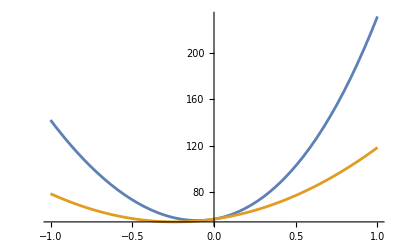

```mathematica
n=3;
x0=RandomReal[{-1,1},n];
dx1=RandomReal[{-1,1},n];
dx2=RandomReal[{-1,1},n];
{f0,df,ddf}=ddRosen[x0,dx1,dx2]
Plot[{Rosen[x0+ϵ dx1],f0+ϵ df+0.5 ϵ^2 ddf},{ϵ,-1,1}]
```